```mathematica
(*Quit[]*)
```

# B_c(p1)→χ_cJ(p2, {α,β}) + W_μ(q)

All form factors

## Init

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/luchinsky/Dropbox/DskD/Work/bc/bc_chi_npi/Math

```mathematica
<<MyPackages`HistV2`
```

```mathematica
chiList = {"chi_c0", "chi_c1", "chi_c2"};
```

```mathematica
<<"./funcs.m"
<<"./mdat/amps.mdat";
<<"./mdat/ebert_ff.mdat";
```

```mathematica
<<"./mdat/numbers.mdat"
```

```mathematica
Clear[BR];
BR::usage="BR[out, outL, ffName] -- my prediction for the branching fraction Bc -> out + outL using FF set ffName (in %)";
Clear[$BR];
$BR::usage="BR[out, outL, ffName] -- prediction for the branching fraction Bc -> out + outL using FF set ffName, presented in the paper (in %)";
```

## Ebert

```mathematica
ffName = "Ebert";
```

```mathematica
<<"mdat/ebert_ff.mdat";
FFRule = ffFitRule
```

{fPlus[q2_]:>0.26826+0.0230397 q2+0.00203804 q2^2+0.000112945 q2^3,fMinus[q2_]:>-0.795038-0.0924677 q2+0.00107262 q2^2-0.00148102 q2^3,hV1[q2_]:>-0.0870429-0.00229868 q2+0.00384674 q2^2-0.000125538 q2^3,hV2[q2_]:>-0.416835-0.100995 q2+0.0137844 q2^2-0.00285859 q2^3,hV3[q2_]:>0.968491+0.153122 q2-0.0140454 q2^2+0.00394357 q2^3,hA[q2_]:>-1.07423-0.124138 q2-0.000875729 q2^2-0.00156938 q2^3,tV[q2_]:>-0.779807-0.141625 q2+0.0166381 q2^2-0.00395881 q2^3,tA1[q2_]:>-0.596459-0.0406516 q2-0.0053293 q2^2-0.00029317 q2^3,tA2[q2_]:>0.0933613-0.0331332 q2+0.0160284 q2^2-0.0022493 q2^3,tA3[q2_]:>0.}

### Two-Body Decays

```mathematica
Clear[$gamma];
$gamma::usage="$gamma[out, outL, type] is the width of Bc -> out outL decay from tables II, VI (in 10^-15GeV)";
$gamma[out_,outL_]:=$gamma[out,outL,"1P"];
(* Table VI *)
$gamma["chi_c0","P"] = 0.23($a1)^2;
$gamma["chi_c0","V"] = 0.64($a1)^2;
$gamma["chi_c1","P"] = 0.22($a1)^2;
$gamma["chi_c1","V"] = 0.16($a1)^2;
$gamma["chi_c2","P"] = 0.41($a1)^2;
$gamma["chi_c2","V"] = 1.18($a1)^2;
```

```mathematica
$BR["chi_c0", "enu", ffName]=0.087;
$BR["chi_c1", "enu", ffName]=0.082;
$BR["chi_c2", "enu", ffName]=0.16;
$BR["chi_c0", "P", ffName]=0.021; $BR["chi_c0", "V", ffName]=0.058;
$BR["chi_c1", "P", ffName]=0.020; $BR["chi_c1", "V", ffName]=0.015;
$BR["chi_c2", "P", ffName]=0.038; $BR["chi_c2", "V", ffName]=0.11;
```

```mathematica
outL="P";
Do[
BR[out, outL, ffName]=10^2 Ngamma[out, outL, FFRule]/gammaTot;
Print["Bc ->"<> out" "<>outL<>":\t this/Ebert=", 10^15 Ngamma[out, outL, ffFitRule]/$gamma[out,outL], "\t Br this/Ebert=", BR[out, outL,ffName]/$BR[out, outL, ffName]]
,{out, chiList}]
```

Bc ->chi_c0  P:	 this/Ebert=0.958573	 Br this/Ebert=1.03364

Bc ->chi_c1  P:	 this/Ebert=0.029722	 Br this/Ebert=0.0321889

Bc ->chi_c2  P:	 this/Ebert=1.01458	 Br this/Ebert=1.07776

```mathematica
outL="V";
Do[
BR[out, outL, ffName]=10^2 Ngamma[out, outL, FFRule]/gammaTot;
Print["Bc ->"<> out" "<>outL<>":\t this/Ebert=", 10^15 Ngamma[out, outL, ffFitRule]/$gamma[out,outL], "\t Br this/Ebert=", BR[out, outL,ffName]/$BR[out, outL, ffName]]
,{out, chiList}]
```

Bc ->chi_c0  V:	 this/Ebert=0.867946	 Br this/Ebert=0.942932

Bc ->chi_c1  V:	 this/Ebert=0.804757	 Br this/Ebert=0.845142

Bc ->chi_c2  V:	 this/Ebert=0.90465	 Br this/Ebert=0.955445

### Semileptonic decays

```mathematica
json = Import["../literatute/Ebert_1007.1369/Fig4.json"];
extractNames[json]
```

{{1,chi_c0_e},{2,chi_c0_tau},{3,chi_c1_e},{4,chi_c1_tau},{5,chi_c2_e},{6,chi_c2_tau}}

```mathematica
Clear[distEE];
distEE::usage="distEE[out, ffName]";
i=1;
Do[
distEE[out, ffName] = extractFF[json, i]["data"];
distEE[out, ffName] = 100*10^-13($Vbc)^2 HST2D[distEE[out,ffName]]/gammaTot;
i += 2;
,{out, chiList}];
```

```mathematica
root = readROOT[getFileName["chi_c0", "enu", "1"], Norm->$BR["chi_c0", "enu", "Ebert"]]
```

⟨ [0.0832354;8.23411],  50 entries⟩

```mathematica
Clear[genENuPlot];
genENuPlot::usage = "genENuPlot[out]";
genENuPlot[out_]:=Module[{},
BR[out, "enu", ffName]=100NIntegrate[Ngamma[out,"enu", ffFitRule],{q2,0,q2Max[out]}]/gammaTot;
Print[out, ": Br[this]/Br[Ebert]=",BR[out, "enu", ffName]/$BR[out, "enu", ffName]];
root=readROOT[getFileName[out, "enu", "1"], Norm-> $BR[out, "enu", ffName]];
Show[
PlotHST@NormalizeHST@distEE[out, ffName],
Plot[100*Ngamma[out,"enu", ffFitRule]/gammaTot/BR[out, "enu", ffName], {q2, 0.2,q2Max[out]}],
PlotHST@NormalizeHST@root,
AxesLabel->{"q2, GeV^2", "1/Γ ⅆΓ/ⅆq^2, 1/GeV^2"}, PlotLabel->out, PlotRange->All]
]
```

chi_c0: Br[this]/Br[Ebert]=1.0214

chi_c1: Br[this]/Br[Ebert]=1.0019

chi_c2: Br[this]/Br[Ebert]=1.00282

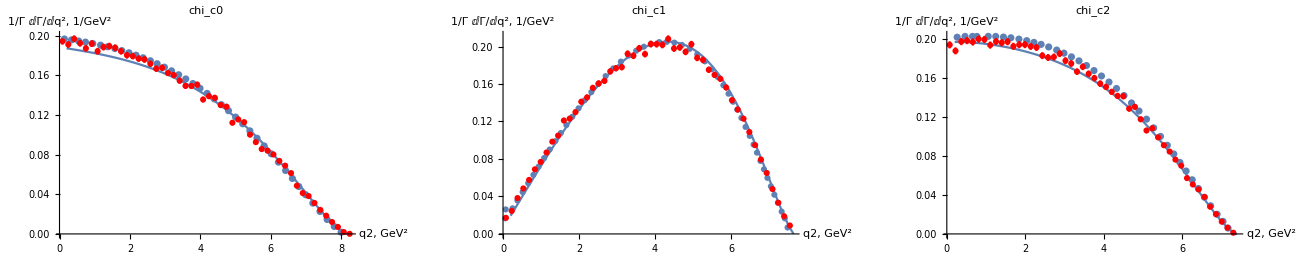

```mathematica
GraphicsGrid[{Table[genENuPlot[out], {out, chiList}]}, ImageSize->1300]
```

### nπ decays

```mathematica
<<"./mdat/rhoT.mdat";
```

```mathematica
rhoL[_]=0;
```

```mathematica
Clear[IdHST];
IdHST[hist_]:=HST2D[Transpose[{hist⟦1,;;,1⟧,hist⟦1,;;,1⟧}]]
```

```mathematica
mode = "3pi";
```

```mathematica
IntegralHST[gg/gammaTot]
```

IntegralHST[7.57576×10^11 gg]

```mathematica
Clear[genNPiPlot];
genNPiPlot::usage="genNPiPlot[out, mPi]";
Options[genNPiPlot] = {PlotStyle->Blue, ShowROOT->True};
genNPiPlot[out_, nPi_, ffName_, OptionsPattern[]]:=Module[{},
FFRule = Switch[ffName, "Ebert", ffFitRule, "Wang", ffFitRule$Wang];
mode = ToString[nPi]<>"pi";react= "Bc→"<>out<>" "<>mode;
BR[out, mode,ffName]= NIntegrate[100/gammaTot Ngamma[out,"W", FFRule]/.{rhoL[_]->0,rhoT[_]->fitRhoT[mode]},{q2, (nPi*$mPi)^2,q2Max[out]}];
Print["Br[",react,"]:=", BR[out, mode,ffName],"%"];
ffNum=Switch[ffName,"Ebert","1","Wang","2"];
root = readROOT[getFileName[out,mode,ffNum],Norm->BR[out, mode,ffName]];
Show[
If[OptionValue[ShowROOT],PlotHST[1.1root],Plot[0, {q2, 0, q2Max[out]}, PlotStyle->Black]],
Plot[1.1*100/gammaTot Ngamma[out,"W", FFRule]/.{rhoL[_]->0,rhoT[_]->fitRhoT[mode]},{q2, (nPi*$mPi)^2,q2Max[out]}, PlotRange->All, PlotStyle->OptionValue[PlotStyle]]
,PlotRange->All, PlotLabel->react]
]
```

Br[Bc→chi_c0 2pi]:=0.0568356%

Br[Bc→chi_c1 2pi]:=0.0154134%

Br[Bc→chi_c2 2pi]:=0.109309%

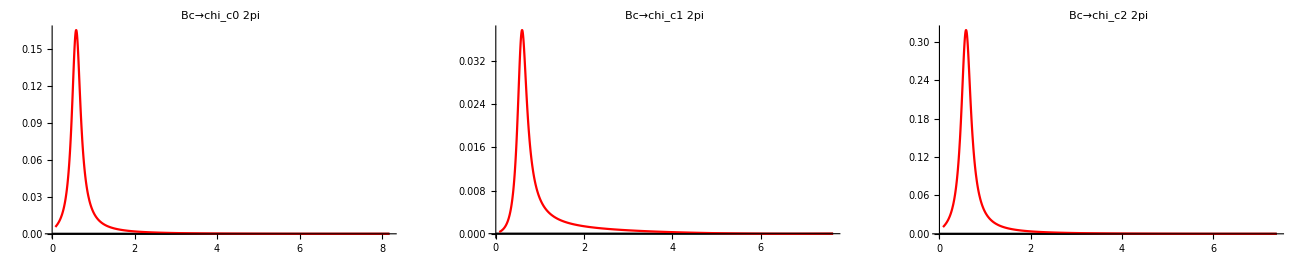

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 2, ffName, PlotStyle->Red, ShowROOT->False],{out,chiList}]}, ImageSize->1300]
```

Br[Bc→chi_c0 2pi]:=0.0568356%

Br[Bc→chi_c1 2pi]:=0.0154134%

Br[Bc→chi_c2 2pi]:=0.109309%

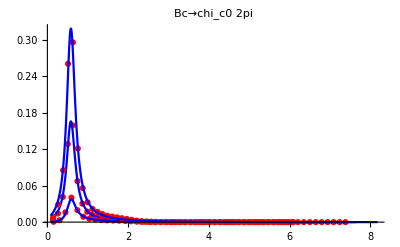

```mathematica
Show[
genNPiPlot["chi_c0", 2, "Ebert"],
genNPiPlot["chi_c1", 2, "Ebert"],
genNPiPlot["chi_c2", 2, "Ebert"]
]
```

Br[Bc→chi_c0 3pi]:=0.0213332%

Br[Bc→chi_c0 3pi]:=0.0213332%

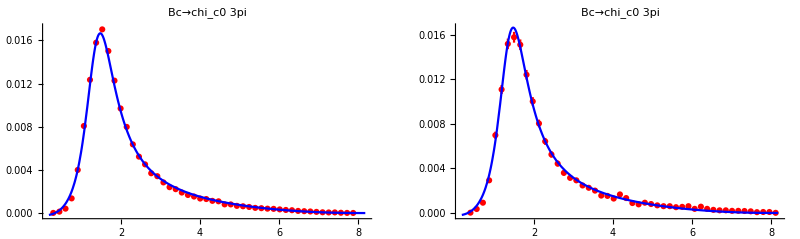

```mathematica
GraphicsGrid[{{
genNPiPlot["chi_c0", 3, "Ebert"],
genNPiPlot["chi_c0", 3, "Wang"]
}}]
```

Br[Bc→chi_c0 3pi]:=0.0213332%

Br[Bc→chi_c1 3pi]:=0.0156027%

Br[Bc→chi_c2 3pi]:=0.0410091%

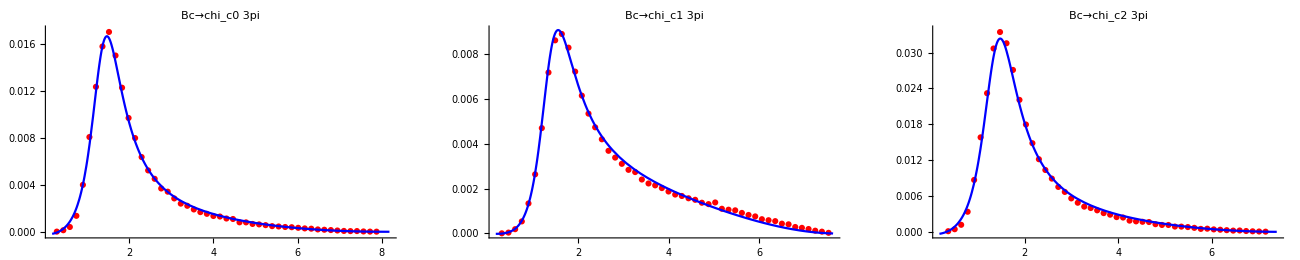

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 3, ffName],{out,chiList}]}, ImageSize->1300]
```

Br[Bc→chi_c0 5pi]:=0.0000379145%

Br[Bc→chi_c1 5pi]:=0.0000486109%

Br[Bc→chi_c2 5pi]:=0.0000670549%

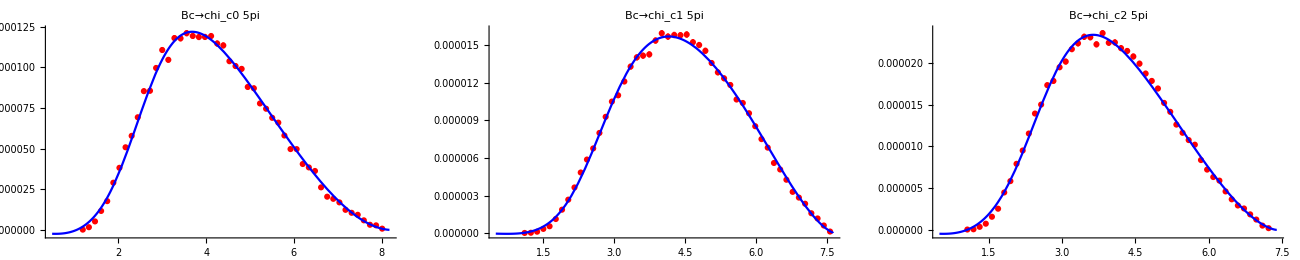

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 5, ffName],{out,chiList}]}, ImageSize->1300]
```

## Wang

```mathematica
ffName = "Wang";
```

```mathematica
<<"./mdat/wang_ff.mdat";
FFRule = ffFitRule$Wang
```

{fPlus[q2_]:>-0.339914-0.0400244 q2+0.002523 q2^2-0.000465616 q2^3,fMinus[q2_]:>0.77019+0.088168 q2-0.00879204 q2^2+0.00108867 q2^3,hV1[q2_]:>-0.244354+0.0103316 q2-0.000913403 q2^2+0.000221592 q2^3,hV2[q2_]:>-0.710388-0.0602775 q2+0.00426655 q2^2-0.000565963 q2^3,hV3[q2_]:>1.49342+0.0899868 q2-0.00685796 q2^2+0.00071155 q2^3,hA[q2_]:>1.27202+0.090039 q2-0.00513732 q2^2+0.000614869 q2^3,tV[q2_]:>1.16583+0.0586233 q2-0.00302289 q2^2+0.000341744 q2^3,tA1[q2_]:>-0.570939-0.0394879 q2+0.00313597 q2^2-0.00039722 q2^3,tA2[q2_]:>-0.168681-0.0274647 q2+0.00572988 q2^2-0.00070363 q2^3,tA3[q2_]:>0.774886+0.0583751 q2-0.000626791 q2^2+0.000196185 q2^3}

### Two-Body Decays

```mathematica
$BR["chi_c0", "enu", ffName]=0.13±0.03;
$BR["chi_c1", "enu", ffName]=0.11±0.03;
$BR["chi_c2", "enu", ffName]=0.10±0.03;
$BR["chi_c0", "P", ffName]=0.031±0.004; $BR["chi_c0", "V", ffName]=0.076±0.009;
$BR["chi_c1", "P", ffName]=0.0021±0.0002; $BR["chi_c1", "V", ffName]=0.023±0.002;
$BR["chi_c2", "P", ffName]=0.021±0.005; $BR["chi_c2", "V", ffName]=0.056±0.011;
```

```mathematica
outL="P";
Do[
BR[out, outL, ffName]=10^2 Ngamma[out, outL, FFRule]/gammaTot;
Print["Bc ->"<> out" "<>outL<> "\t Br this/Ebert=", BR[out, outL,ffName]/$BR[out, outL, ffName]]
,{out, chiList}]
```

Bc ->chi_c0  P	 Br this/Ebert=1.12673±0.145384

Bc ->chi_c1  P	 Br this/Ebert=1.33885±0.127509

Bc ->chi_c2  P	 Br this/Ebert=1.13559±0.270379

```mathematica
outL="V";
Do[
BR[out, outL, ffName]=10^2 Ngamma[out, outL, FFRule]/gammaTot;
Print["Bc ->"<> out" "<>outL<> "\t Br this/Ebert=", BR[out, outL,ffName]/$BR[out, outL, ffName]]
,{out, chiList}]
```

Bc ->chi_c0  V	 Br this/Ebert=1.18608±0.140457

Bc ->chi_c1  V	 Br this/Ebert=1.17051±0.101784

Bc ->chi_c2  V	 Br this/Ebert=1.17124±0.230065

### Semileptonic decays

```mathematica
Clear[extractNames];
extractNames[json_]:=Module[{names = json⟦3,2,All,1,2⟧}, Table[{i,names⟦i⟧},{i,Length[names]}]];
```

```mathematica
json = Import["../literatute/1107.0474/Fig5_e.json"];
names = extractNames[json]
```

{{1,chi_c0},{2,chi_c1},{3,chi_c2}}

```mathematica
Clear[genEnuPlot]
genEnuPlot::usage="genEnuPlot[out]";
genENuPlot[out_]:=Module[{},
BR[out, "enu",ffName] = NIntegrate[100/gammaTot Ngamma[out,"enu", FFRule],{q2, 0, q2Max[out]}] ;
root = readROOT[getFileName[out,"enu","2",Var->"m2_0m1"], Norm->1];
PlotQ2 = Show[
Plot[100/gammaTot Ngamma[out,"enu", FFRule]/BR[out, "enu",ffName], {q2, 0.2,q2Max[out]}],
PlotHST[root]
, AxesLabel->{"q2, GeV^2", "~ⅆΓ/dq2"}, PlotLabel->"Bc -> "<>out<>"e nu"];
pap =NormalizeHST@HST2D[extractFF[json, Select[names, #⟦2⟧==out&][[1,1]]]["data"]];
root = readROOT[getFileName[out,"enu","2",Var->"e_2"], Norm->1];
PlotEE = Show[
PlotHST[pap, Joined->True], PlotHST[root]
,AxesLabel->{"Ee, GeV", "1/Γ ⅆΓ/ⅆEe"}, PlotLabel->"Bc -> "<>out<>"e nu"];
Print["Br[Bc->"<>out<>"+enu]=",BR[out, "enu",ffName],"\t this/Wang=",BR[out, "enu",ffName]/$BR[out, "enu",ffName]];
GraphicsGrid[{{PlotQ2, PlotEE}}, ImageSize->1000]
];
```

Br[Bc->chi_c0+enu]=0.137511	 this/Wang=1.05777±0.244102

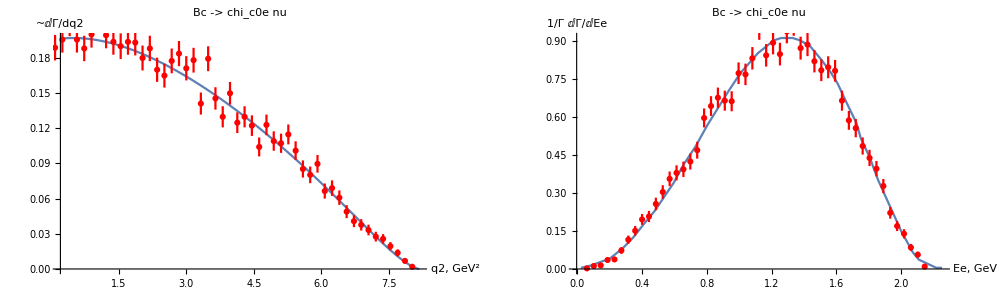

```mathematica
genENuPlot["chi_c0"]
```

Br[Bc->chi_c1+enu]=0.114656	 this/Wang=1.04232±0.28427

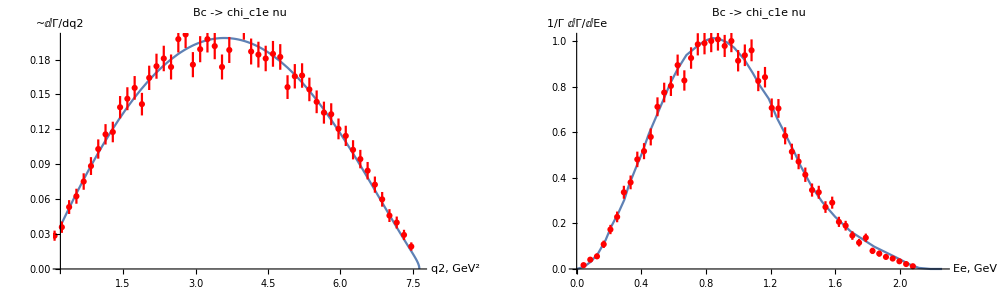

```mathematica
genENuPlot["chi_c1"]
```

Br[Bc->chi_c2+enu]=0.0971092	 this/Wang=0.971092±0.291327

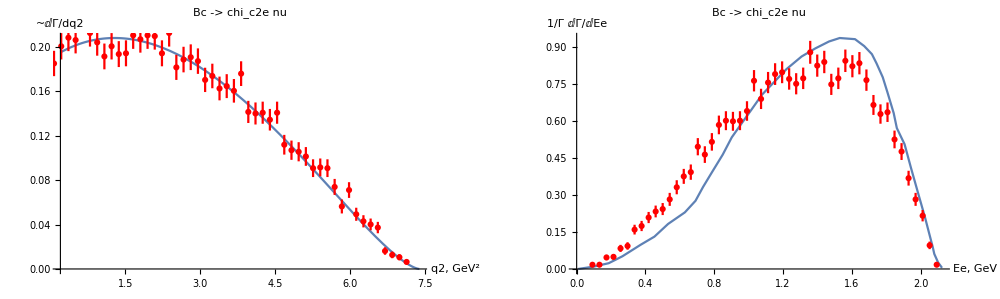

```mathematica
genENuPlot["chi_c2"]
```

### nπ decays

Br[Bc→chi_c0 2pi]:=0.0935369%

Br[Bc→chi_c1 2pi]:=0.0311114%

Br[Bc→chi_c2 2pi]:=0.0683901%

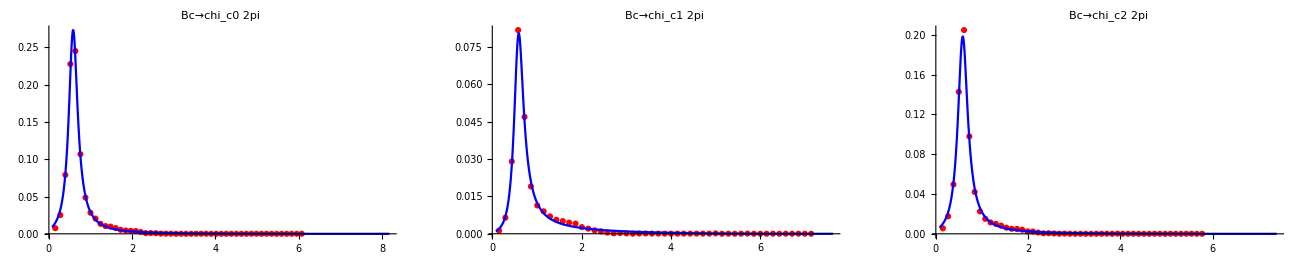

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 2, ffName],{out,chiList}]}, ImageSize->1300]
```

Br[Bc→chi_c0 3pi]:=0.0344526%

Br[Bc→chi_c1 3pi]:=0.0249461%

Br[Bc→chi_c2 3pi]:=0.0262385%

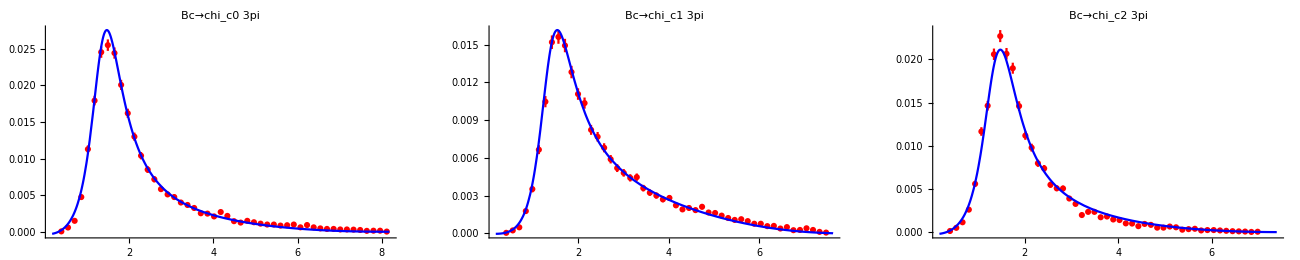

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 3, ffName],{out,chiList}]}, ImageSize->1300]
```

Br[Bc→chi_c0 5pi]:=0.0000564033%

Br[Bc→chi_c1 5pi]:=0.0000634153%

Br[Bc→chi_c2 5pi]:=0.0000391096%

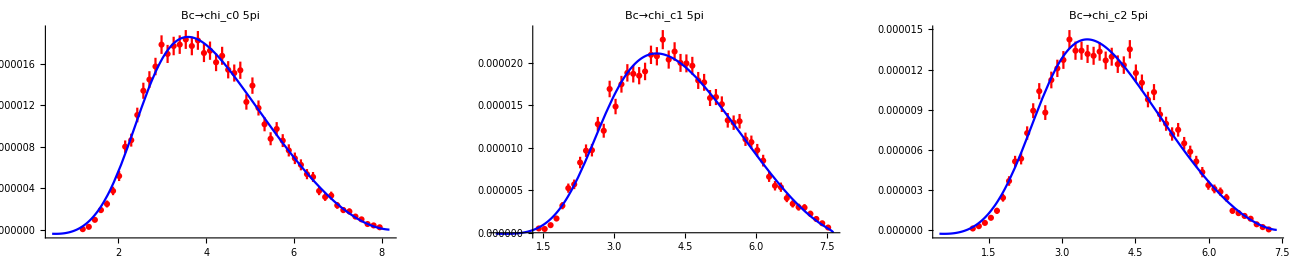

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 5, ffName],{out,chiList}]}, ImageSize->1300]
```

## Saving

```mathematica
<<"funcs.m"
```

```mathematica
SaveVar["./mdat/branchings.mdat", BR];
SaveVar["./mdat/branchings.mdat", $BR, Overwrite->False];
```

## Corrections

```mathematica
Clear[corrCoeff];
corrCoeff::usage="corrFF[out, outL, ffName] = √($BR/BR): I need to multiply FFs by this coefficient in order to get enu branchings from the papers";
```

```mathematica
Do[
corrCoeff[out, ffName]=√($BR[out, "enu", ffName]/BR[out, "enu", ffName]);
Print["corr[",out,",",ffName,"]=",GetCentralValue[corrCoeff[out, ffName]]];
,{out, chiList},{ffName,{"Ebert","Wang"}}];
Print["Mean correction (all but chi_c2, Wang): ",
Mean[#]± √Variance[#]&@Drop[#,-1]&@
GetCentralValue@Flatten@
Table[corrCoeff[out, ffName],{out, chiList},{ffName,{"Ebert","Wang"}}]
]
```

corr[chi_c0,Ebert]=0.989466

corr[chi_c0,Wang]=0.972308

corr[chi_c1,Ebert]=0.999054

corr[chi_c1,Wang]=0.979486

corr[chi_c2,Ebert]=0.998592

corr[chi_c2,Wang]=1.01478

Mean correction (all but chi_c2, Wang): 0.987781±0.0117795

```mathematica
SaveVar["./mdat/corrCoeff.mdat", corrCoeff]
```

```mathematica
Clear[corrBR];
corrBR::usage="corrBR[out, outL, ffName] is my prediction for the branching fraction with correction";
corrBR[out_, outL_, ffName_]:=corrCoeff[out, ffName]^2 BR[out, outL, ffName];
```

```mathematica
Unprotect[Round];
Round[a_±b_,e_]:=Round[a,e]±Round[b,e]
```

## Presentations

```mathematica
Clear[SaveFig];
Options[SaveFig]={Save->True};
SaveFig[name_, plot_, OptionsPattern[]]:=Module[{fileName="../TeX/presentation/figs/"<>name<>".pdf"},
If[OptionValue[Save],
Print["Saving figure to ", fileName];
Export[fileName, plot],
Print["Saving disabled"]
]
]
```

```mathematica
Clear[createCompTable];
createCompTable::usage="createCompTable[out, mode, ffName]";
createCompTable[out_, mode_, ffName_, eps_:0.001]:=Module[{},
brPap = ToString[Round[$BR[out, mode, ffName], eps], TeXForm];
(*brMy = ToString[Round[corrCoeff[out, ffName]^2*BR[out, mode, ffName], eps], TeXForm];*)
brMy = ToString[Round[BR[out, mode, ffName], eps], TeXForm];
rat = ToString[Round[BR[out, mode, ffName]/$BR[out, mode, ffName],eps], TeXForm];
str ="% Bc -> "<>out<>" + "<>mode <>" with ["<>ffName<>"]\n";
str = str<> 
"      \\begin{tabular}{lcr}
          Paper &:& $\\Br  = "<>brPap<>"\\%$ \\\\
          this      &:& $\\Br  = "<>brMy<>"\\%$ \\\\
		  ratio   &:& $"<>rat<>"$ \\\\
      \\end{tabular}
";
(* saving *)
fileName = "../TeX/presentation/tables/"<>out<>"_"<>mode<>"_"<>ffName<>".tex";
file = OpenWrite[fileName];
Print["Saving to file ", fileName];
WriteString[file, str];
Close[file];
Return[str];
]
```

### form factors

```mathematica
Clear[genFFplot];
Options[genFFplot]={Factors->{1,1}};
genFFplot[func_,name_, out_, OptionsPattern[]]:=Module[{factors=OptionValue[Factors]},
Plot[
{factors⟦1⟧*corrCoeff[out,"Ebert"]*func[q2]/.ffFitRule,
factors⟦2⟧*GetCentralValue[corrCoeff[out,"Wang"]]func[q2]/.ffFitRule$Wang},
{q2, 0, q2Max[out]},
Frame->True,
FrameLabel->{"q^2, GeV^2", name<>"(q^2)"}, AxesOrigin->{0,0},
GridLines->Automatic,
PlotStyle->{Red, Blue}
]
]
```

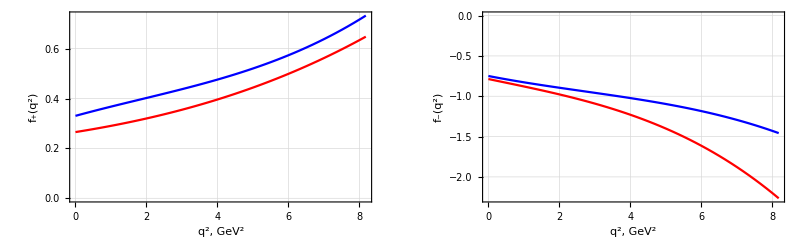

Saving figure to ../TeX/presentation/figs/ff_chi_c0.pdf

```mathematica
out="chi_c0";
plt = Show[
GraphicsGrid[{{
genFFplot[fPlus, "f_+",out, Factors->{1,-1}],
genFFplot[fMinus, "f_-",out, Factors->{1,-1}]
}}]
,
Epilog->Inset[Row[{
LineLegend[{Red},{"[Ebert]"}],
LineLegend[{Blue},{"[Wang]"}]
}],Offset[{300,20},{20,0.14}]]
,PlotRange->{All, {-200, 50}}]
SaveFig["ff_"<>out, plt];
```

chi_c1

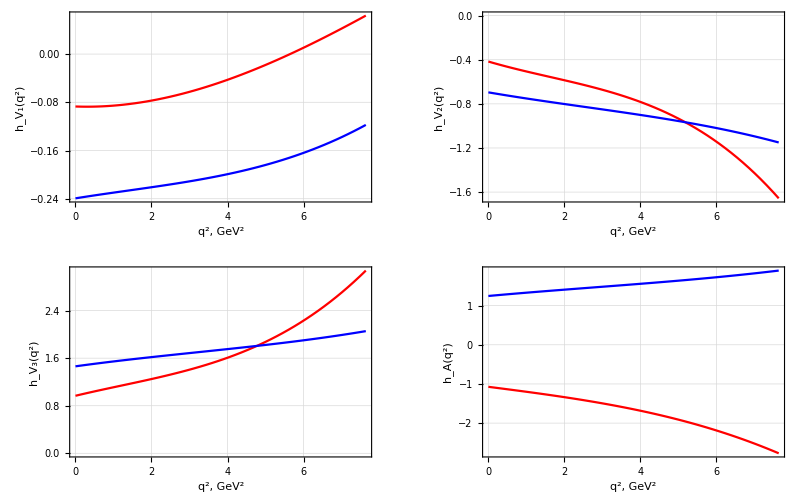

Saving figure to ../TeX/presentation/figs/ff_chi_c1.pdf

```mathematica
out="chi_c1"
plt = Show[GraphicsGrid[{
{genFFplot[hV1,"h_V_1", out], genFFplot[hV2,"h_V_2", out]},
{genFFplot[hV3,"h_V_3", out], genFFplot[hA,"h_A", out]}
}],
Epilog->Inset[Row[{
LineLegend[{Red},{"[Ebert]"}],
LineLegend[{Blue},{"[Wang]"}]
}],Offset[{300,10},{-20,0.14}]]
,PlotRange->{All, {-500, 30}}
]
SaveFig["ff_"<>out, plt];
```

chi_c2

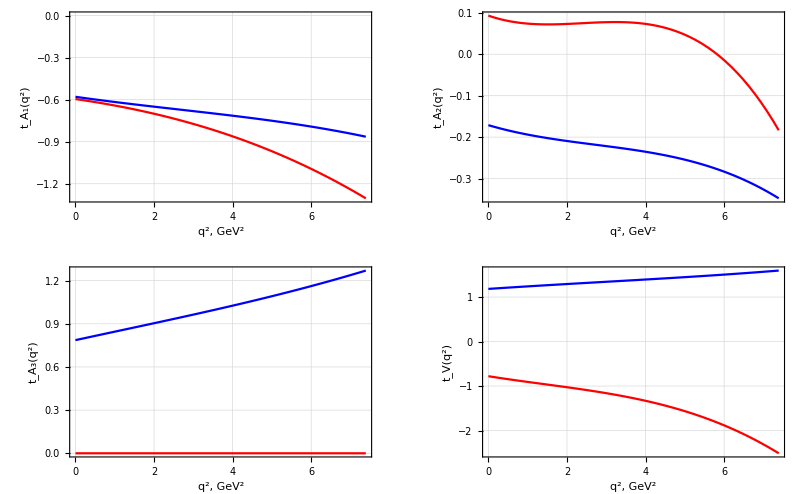

Saving figure to ../TeX/presentation/figs/ff_chi_c2.pdf

```mathematica
out="chi_c2"
plt = Show[GraphicsGrid[{
{genFFplot[tA1,"t_A_1", out], genFFplot[tA2,"t_A_2", out]},
{genFFplot[tA3,"t_A_3", out], genFFplot[tV,"t_V", out]}
}],
Epilog->Inset[Row[{
LineLegend[{Red},{"[Ebert]"}],
LineLegend[{Blue},{"[Wang]"}]
}],Offset[{300,10},{-20,0.14}]]
,PlotRange->{All, {-500, 30}}
]
SaveFig["ff_"<>out, plt];
```

### spectral functions

```mathematica
Clear[getRhoTPlot];
getRhoTPlot::usage="getRhoTPlot[out, mode, ff, XRange->{0,1}]";
Options[getRhoTPlot]={XRange->{0, 3}};
getRhoTPlot[out_, mode_, ff_, OptionsPattern[]]:=Module[{xRange=OptionValue[XRange], rrr},
Show[
Plot[fitRhoT[mode], {q2, 0, xRange⟦2⟧},PlotRange-> All],
(*PlotHST[rrr, Joined->True, ShowErrors->False, PlotRange->{{0, xRange⟦2⟧},{0, 1.1*Max[rrr⟦1,;;,2⟧]}}], *)
AxesOrigin->{0,0},
Frame->True, FrameLabel->{"q^2, GeV^2", "~ρ_T(q^2)"},
GridLines->Automatic,
PlotLabel->mode]
]
```

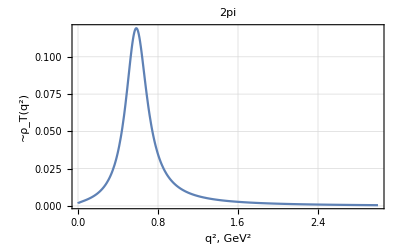

Saving figure to ../TeX/presentation/figs/rhoT_2pi_q2.pdf

```mathematica
mode = "2pi";
getRhoTPlot["chi_c0", mode, "1"]
SaveFig["rhoT"<>"_"<>mode<>"_q2", %];
```

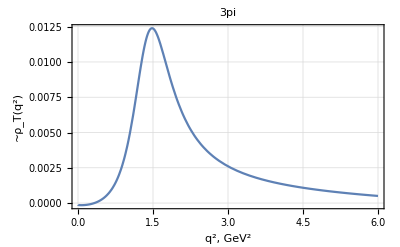

Saving figure to ../TeX/presentation/figs/rhoT_3pi_q2.pdf

```mathematica
mode = "3pi";
getRhoTPlot["chi_c0", mode, "1", XRange->{0, 6}]
SaveFig["rhoT"<>"_"<>mode<>"_q2", %];
```

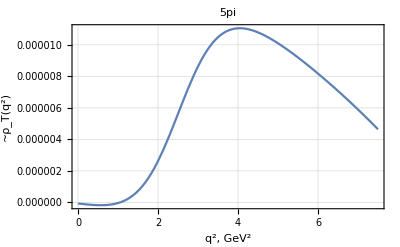

Saving figure to ../TeX/presentation/figs/rhoT_5pi_q2.pdf

```mathematica
mode = "5pi";
getRhoTPlot["chi_c1", mode, "1", XRange->{0, 7.5}]
SaveFig["rhoT"<>"_"<>mode<>"_q2", %];
```

### eν

#### χ_c0

```mathematica
out = "chi_c0";
```

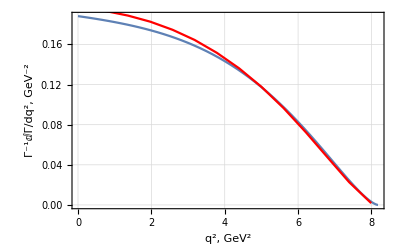

Saving figure to ../TeX/presentation/figs/chi_c0_enu_q2_Ebert.pdf

../TeX/presentation/figs/chi_c0_enu_q2_Ebert.pdf

```mathematica
(* Ebert, q2 *)
out="chi_c0";
norm = NIntegrate[Ngamma[out, "enu",ffFitRule],{q2,0,q2Max[out]}];
papTable = NormalizeHST[distEE["chi_c0","Ebert"]];
papTable =HST2D[papTable⟦1,;; ;;3⟧];
plt = Show[
Plot[Ngamma[out, "enu",ffFitRule]/norm,{q2,0,q2Max[out]}],
PlotHST[papTable, PlotStyle->Red, Joined->True]
,Frame->True, GridLines->Automatic
 ,FrameLabel->{"q^2, GeV^2", "Γ^-1ⅆΓ/dq^2, GeV^-2"},
Epilog->Inset[Framed[Column[{
LineLegend[{Blue},{"this"}],
LineLegend[{Red},{"paper"}]
}]],Offset[{10,20},{7.0,0.14}]]]
SaveFig[out<>"_enu_q2_Ebert", plt]
```

```mathematica
createCompTable[out, "enu", "Ebert"]
```

Saving to file ../TeX/presentation/tables/chi_c0_enu_Ebert.tex

% Bc -> chi_c0 + enu with [Ebert]
      \begin{tabular}{lcr}
          Paper &:& $\Br  = 0.087\%$ \\
          this      &:& $\Br  = 0.089\%$ \\
		  ratio   &:& $1.021$ \\
      \end{tabular}

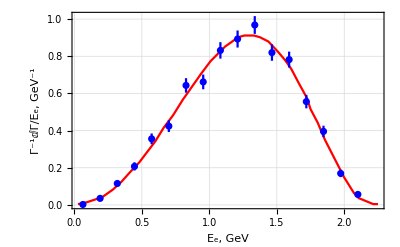

Saving figure to ../TeX/presentation/figs/chi_c0_enu_e2_Wang.pdf

../TeX/presentation/figs/chi_c0_enu_e2_Wang.pdf

```mathematica
(* Wang, e2 *)
out="chi_c0";
root = readROOT[getFileName[out,"enu","2",Var->"e_2"], Norm->1];
root = HST2D@root⟦1,;;;;3⟧;
pap =NormalizeHST@HST2D[extractFF[json, Select[names, #⟦2⟧==out&][[1,1]]]["data"]];
plt = Show[
PlotHST[pap, PlotStyle->Red, Joined->True],
PlotHST[root, PlotStyle->Blue]
,PlotRange->All
,Frame->True, GridLines->Automatic
 ,FrameLabel->{"E_e, GeV", "Γ^-1ⅆΓ/E_e, GeV^-1"},
Epilog->Inset[Framed[Column[{
LineLegend[{Red},{"paper"}],
PointLegend[{Blue},{"this"}]
}]],Offset[{10,20},{1.95,0.75}]]]
SaveFig[out<>"_enu_e2_Wang", plt]
```

```mathematica
createCompTable[out, "enu", "Wang"]
```

Saving to file ../TeX/presentation/tables/chi_c0_enu_Wang.tex

% Bc -> chi_c0 + enu with [Wang]
      \begin{tabular}{lcr}
          Paper &:& $\Br  = 0.13\pm 0.03\%$ \\
          this      &:& $\Br  = 0.138\%$ \\
		  ratio   &:& $1.058\pm 0.244$ \\
      \end{tabular}

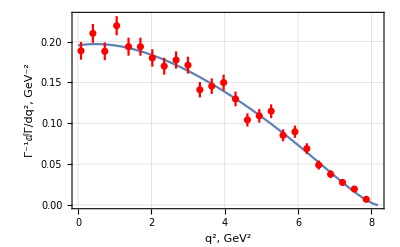

Saving figure to ../TeX/presentation/figs/chi_c0_enu_q2_Wang.pdf

../TeX/presentation/figs/chi_c0_enu_q2_Wang.pdf

```mathematica
(* Wang, q2 *)
out="chi_c0";
norm = NIntegrate[Ngamma[out, "enu",ffFitRule$Wang],{q2,0,q2Max[out]}];
root = readROOT[getFileName[out, "enu", "2"], Norm->1];
root = HST2D@root⟦1,;;;;2⟧;
plt = Show[
Plot[Ngamma[out, "enu",ffFitRule$Wang]/norm,{q2,0,q2Max[out]}],
PlotHST[root, PlotStyle->Red]
,Frame->True, GridLines->Automatic
 ,FrameLabel->{"q^2, GeV^2", "Γ^-1ⅆΓ/dq^2, GeV^-2"},
PlotRange->All,
Epilog->Inset[Framed[Column[{
LineLegend[{Blue},{"this"}],
PointLegend[{Red},{"ROOT"}]
}]],Offset[{10,20},{7.0,0.17}]]
]
SaveFig[out<>"_enu_q2_Wang", plt]
```

#### χ_c1

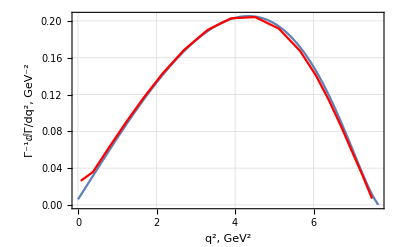

Saving figure to ../TeX/presentation/figs/chi_c1_enu_q2_Ebert.pdf

../TeX/presentation/figs/chi_c1_enu_q2_Ebert.pdf

```mathematica
(* Ebert, q2 *)
out="chi_c1";
norm = NIntegrate[Ngamma[out, "enu",ffFitRule],{q2,0,q2Max[out]}];
papTable = NormalizeHST[distEE[out,"Ebert"]];
papTable =HST2D[papTable⟦1,;; ;;3⟧];
plt = Show[
Plot[Ngamma[out, "enu",ffFitRule]/norm,{q2,0,q2Max[out]}],
PlotHST[papTable, PlotStyle->Red, Joined->True]
,Frame->True, GridLines->Automatic
 ,FrameLabel->{"q^2, GeV^2", "Γ^-1ⅆΓ/dq^2, GeV^-2"},
Prolog->Inset[Framed[Column[{
LineLegend[{Blue},{"this"}],
LineLegend[{Red},{"paper"}]
}]],Offset[{10,20},{6.6,0.15}]]]
SaveFig[out<>"_enu_q2_Ebert", plt]
```

```mathematica
createCompTable[out, "enu", "Ebert"]
```

Saving to file ../TeX/presentation/tables/chi_c1_enu_Ebert.tex

% Bc -> chi_c1 + enu with [Ebert]
      \begin{tabular}{lcr}
          Paper &:& $\Br  = 0.082\%$ \\
          this      &:& $\Br  = 0.082\%$ \\
		  ratio   &:& $1.002$ \\
      \end{tabular}

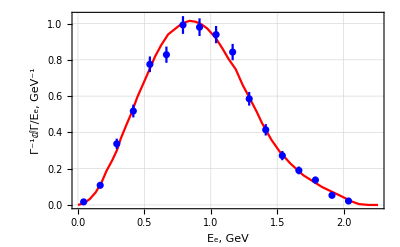

Saving figure to ../TeX/presentation/figs/chi_c1_enu_e2_Wang.pdf

../TeX/presentation/figs/chi_c1_enu_e2_Wang.pdf

```mathematica
(* Wang, e2 *)
out="chi_c1";
root = readROOT[getFileName[out,"enu","2",Var->"e_2"], Norm->1];
root = HST2D@root⟦1,;;;;3⟧;
pap =NormalizeHST@HST2D[extractFF[json, Select[names, #⟦2⟧==out&][[1,1]]]["data"]];
plt = Show[
PlotHST[pap, PlotStyle->Red, Joined->True],
PlotHST[root, PlotStyle->Blue]
,PlotRange->All
,Frame->True, GridLines->Automatic
 ,FrameLabel->{"E_e, GeV", "Γ^-1ⅆΓ/E_e, GeV^-1"},
Epilog->Inset[Framed[Column[{
LineLegend[{Red},{"paper"}],
PointLegend[{Blue},{"this"}]
}]],Offset[{10,20},{1.95,0.75}]]]
SaveFig[out<>"_enu_e2_Wang", plt]
```

```mathematica
createCompTable[out, "enu", "Wang"]
```

Saving to file ../TeX/presentation/tables/chi_c1_enu_Wang.tex

% Bc -> chi_c1 + enu with [Wang]
      \begin{tabular}{lcr}
          Paper &:& $\Br  = 0.11\pm 0.03\%$ \\
          this      &:& $\Br  = 0.115\%$ \\
		  ratio   &:& $1.042\pm 0.284$ \\
      \end{tabular}

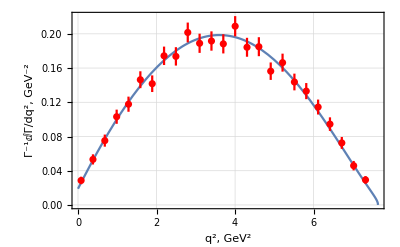

Saving figure to ../TeX/presentation/figs/chi_c1_enu_q2_Wang.pdf

../TeX/presentation/figs/chi_c1_enu_q2_Wang.pdf

```mathematica
(* Wang, q2 *)
out="chi_c1";
norm = NIntegrate[Ngamma[out, "enu",ffFitRule$Wang],{q2,0,q2Max[out]}];
root = readROOT[getFileName[out, "enu", "2"], Norm->1];
root = HST2D@root⟦1,;;;;2⟧;
plt = Show[
Plot[Ngamma[out, "enu",ffFitRule$Wang]/norm,{q2,0,q2Max[out]}],
PlotHST[root, PlotStyle->Red]
,Frame->True, GridLines->Automatic
 ,FrameLabel->{"q^2, GeV^2", "Γ^-1ⅆΓ/dq^2, GeV^-2"},
PlotRange->All,
Epilog->Inset[Framed[Column[{
LineLegend[{Blue},{"this"}],
PointLegend[{Red},{"ROOT"}]
}]],Offset[{10,20},{6.6,0.16}]]
]
SaveFig[out<>"_enu_q2_Wang", plt]
```

#### χ_c2

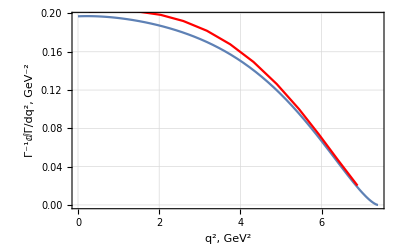

Saving figure to ../TeX/presentation/figs/chi_c2_enu_q2_Ebert.pdf

../TeX/presentation/figs/chi_c2_enu_q2_Ebert.pdf

```mathematica
(* Ebert, q2 *)
out="chi_c2";
norm = NIntegrate[Ngamma[out, "enu",ffFitRule],{q2,0,q2Max[out]}];
papTable = NormalizeHST[distEE[out,"Ebert"]];
papTable =HST2D[papTable⟦1,;; ;;3⟧];
plt = Show[
Plot[Ngamma[out, "enu",ffFitRule]/norm,{q2,0,q2Max[out]}],
PlotHST[papTable, PlotStyle->Red, Joined->True]
,Frame->True, GridLines->Automatic
 ,FrameLabel->{"q^2, GeV^2", "Γ^-1ⅆΓ/dq^2, GeV^-2"},
Prolog->Inset[Framed[Column[{
LineLegend[{Blue},{"this"}],
LineLegend[{Red},{"paper"}]
}]],Offset[{10,20},{6.3,0.145}]]]
SaveFig[out<>"_enu_q2_Ebert", plt]
```

```mathematica
createCompTable[out, "enu", "Ebert"]
```

Saving to file ../TeX/presentation/tables/chi_c2_enu_Ebert.tex

% Bc -> chi_c2 + enu with [Ebert]
      \begin{tabular}{lcr}
          Paper &:& $\Br  = 0.16\%$ \\
          this      &:& $\Br  = 0.16\%$ \\
		  ratio   &:& $1.003$ \\
      \end{tabular}

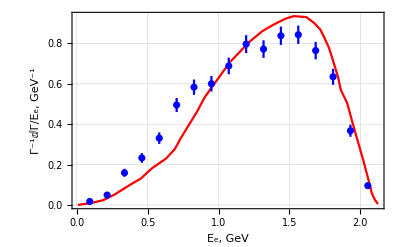

Saving figure to ../TeX/presentation/figs/chi_c2_enu_e2_Wang.pdf

../TeX/presentation/figs/chi_c2_enu_e2_Wang.pdf

```mathematica
(* Wang, e2 *)
out="chi_c2";
root = readROOT[getFileName[out,"enu","2",Var->"e_2"], Norm->1];
root = HST2D@root⟦1,;;;;3⟧;
pap =NormalizeHST@HST2D[extractFF[json, Select[names, #⟦2⟧==out&][[1,1]]]["data"]];
plt = Show[
PlotHST[pap, PlotStyle->Red, Joined->True],
PlotHST[root, PlotStyle->Blue]
,PlotRange->All
,Frame->True, GridLines->Automatic
 ,FrameLabel->{"E_e, GeV", "Γ^-1ⅆΓ/E_e, GeV^-1"},
Epilog->Inset[Framed[Column[{
LineLegend[{Red},{"paper"}],
PointLegend[{Blue},{"this"}]
}]],Offset[{10,20},{0.2,0.7}]]]
SaveFig[out<>"_enu_e2_Wang", plt]
```

```mathematica
createCompTable[out, "enu", "Wang"]
```

Saving to file ../TeX/presentation/tables/chi_c2_enu_Wang.tex

% Bc -> chi_c2 + enu with [Wang]
      \begin{tabular}{lcr}
          Paper &:& $\Br  = 0.1\pm 0.03\%$ \\
          this      &:& $\Br  = 0.097\%$ \\
		  ratio   &:& $0.971\pm 0.291$ \\
      \end{tabular}

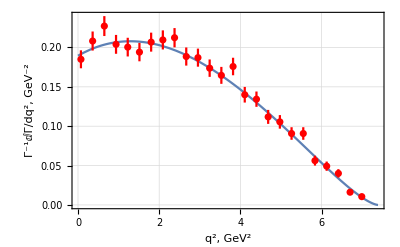

Saving figure to ../TeX/presentation/figs/chi_c2_enu_q2_Wang.pdf

../TeX/presentation/figs/chi_c2_enu_q2_Wang.pdf

```mathematica
(* Wang, q2 *)
out="chi_c2";
norm = NIntegrate[Ngamma[out, "enu",ffFitRule$Wang],{q2,0,q2Max[out]}];
root = readROOT[getFileName[out, "enu", "2"], Norm->1];
root = HST2D@root⟦1,;;;;2⟧;
plt = Show[
Plot[Ngamma[out, "enu",ffFitRule$Wang]/norm,{q2,0,q2Max[out]}],
PlotHST[root, PlotStyle->Red]
,Frame->True, GridLines->Automatic
 ,FrameLabel->{"q^2, GeV^2", "Γ^-1ⅆΓ/dq^2, GeV^-2"},
PlotRange->All,
Epilog->Inset[Framed[Column[{
LineLegend[{Blue},{"this"}],
PointLegend[{Red},{"ROOT"}]
}]],Offset[{10,20},{6.45,0.175}]]
]
SaveFig[out<>"_enu_q2_Wang", plt]
```

### ρ

```mathematica
$mV=0.770GeV;
```

#### χ_c0

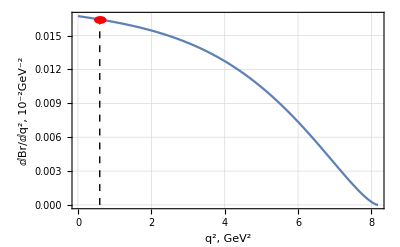

Saving figure to ../TeX/presentation/figs/chi_c0_enu_rho_Ebert.pdf

../TeX/presentation/figs/chi_c0_enu_rho_Ebert.pdf

Saving to file ../TeX/presentation/tables/chi_c0_V_Ebert.tex

% Bc -> chi_c0 + V with [Ebert]
      \begin{tabular}{lcr}
          Paper &:& $\Br  = 0.058\%$ \\
          this      &:& $\Br  = 0.055\%$ \\
		  ratio   &:& $0.943$ \\
      \end{tabular}

```mathematica
out = "chi_c0";
plt = Show[
Plot[100  Ngamma[out, "enu", ffFitRule]/gammaTot,{q2,0,q2Max[out]}],
Graphics[{Dashed, Line[{{($mV)^2,0},{($mV)^2,1}}],
Red, Disk[{($mV)^2,100  Ngamma[out, "enu", ffFitRule]/gammaTot/.{q2->($mV)^2}},Scaled[0.02]]
}]
,Frame->True, FrameLabel->{"q^2, GeV^2","ⅆBr/ⅆq^2, 10^-2GeV^-2"},
GridLines->Automatic
]
SaveFig[out<>"_enu_rho_Ebert", plt]
createCompTable[out, "V", "Ebert"]
```

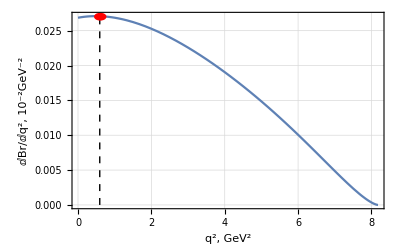

Saving figure to ../TeX/presentation/figs/chi_c0_enu_rho_Wang.pdf

../TeX/presentation/figs/chi_c0_enu_rho_Wang.pdf

Saving to file ../TeX/presentation/tables/chi_c0_V_Wang.tex

% Bc -> chi_c0 + V with [Wang]
      \begin{tabular}{lcr}
          Paper &:& $\Br  = 0.076\pm 0.009\%$ \\
          this      &:& $\Br  = 0.09\%$ \\
		  ratio   &:& $1.186\pm 0.14$ \\
      \end{tabular}

```mathematica
out = "chi_c0";
plt = Show[
Plot[100  Ngamma[out, "enu", ffFitRule$Wang]/gammaTot,{q2,0,q2Max[out]}],
Graphics[{Dashed, Line[{{($mV)^2,0},{($mV)^2,1}}],
Red, Disk[{($mV)^2,100  Ngamma[out, "enu", ffFitRule$Wang]/gammaTot/.{q2->($mV)^2}},Scaled[0.02]]
}]
,Frame->True, FrameLabel->{"q^2, GeV^2","ⅆBr/ⅆq^2, 10^-2GeV^-2"},
GridLines->Automatic
]
SaveFig[out<>"_enu_rho_Wang", plt]
createCompTable[out, "V", "Wang"]
```

```mathematica
out = "chi_c0";
plt = Show[
Plot[100  Ngamma[out, "enu", ffFitRule]/gammaTot,{q2,0,q2Max[out]}],
Graphics[{Dashed, Line[{{($mV)^2,0},{($mV)^2,1}}],
Red, Disk[{($mV)^2,100  Ngamma[out, "enu", ffFitRule]/gammaTot/.{q2->($mV)^2}},Scaled[0.02]]
}]
,Frame->True, FrameLabel->{"q^2, GeV^2","ⅆBr/ⅆq^2, 10^-2GeV^-2"},
GridLines->Automatic
]
SaveFig[out<>"_enu_rho_Ebert", plt]
```

-Graphics-

Saving figure to ../TeX/presentation/figs/chi_c0_enu_rho_Ebert.pdf

../TeX/presentation/figs/chi_c0_enu_rho_Ebert.pdf

#### χ_c1

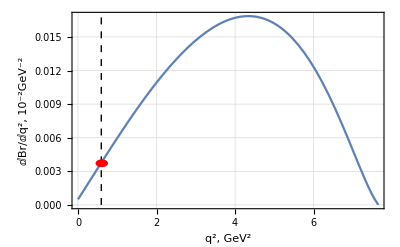

Saving figure to ../TeX/presentation/figs/chi_c1_enu_rho_Ebert.pdf

../TeX/presentation/figs/chi_c1_enu_rho_Ebert.pdf

Saving to file ../TeX/presentation/tables/chi_c1_V_Ebert.tex

% Bc -> chi_c1 + V with [Ebert]
      \begin{tabular}{lcr}
          Paper &:& $\Br  = 0.015\%$ \\
          this      &:& $\Br  = 0.013\%$ \\
		  ratio   &:& $0.845$ \\
      \end{tabular}

```mathematica
out = "chi_c1";
plt = Show[
Plot[100  Ngamma[out, "enu", ffFitRule]/gammaTot,{q2,0,q2Max[out]}],
Graphics[{Dashed, Line[{{($mV)^2,0},{($mV)^2,1}}],
Red, Disk[{($mV)^2,100  Ngamma[out, "enu", ffFitRule]/gammaTot/.{q2->($mV)^2}},Scaled[0.02]]
}]
,Frame->True, FrameLabel->{"q^2, GeV^2","ⅆBr/ⅆq^2, 10^-2GeV^-2"},
GridLines->Automatic
]
SaveFig[out<>"_enu_rho_Ebert", plt]
createCompTable[out, "V", "Ebert"]
```

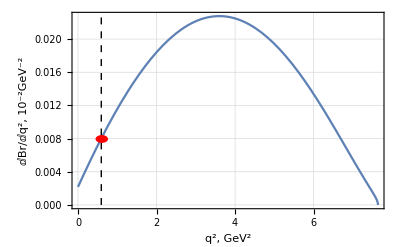

Saving figure to ../TeX/presentation/figs/chi_c1_enu_rho_Wang.pdf

../TeX/presentation/figs/chi_c1_enu_rho_Wang.pdf

Saving to file ../TeX/presentation/tables/chi_c1_V_Wang.tex

% Bc -> chi_c1 + V with [Wang]
      \begin{tabular}{lcr}
          Paper &:& $\Br  = 0.023\pm 0.002\%$ \\
          this      &:& $\Br  = 0.027\%$ \\
		  ratio   &:& $1.171\pm 0.102$ \\
      \end{tabular}

```mathematica
out = "chi_c1";
plt = Show[
Plot[100  Ngamma[out, "enu", ffFitRule$Wang]/gammaTot,{q2,0,q2Max[out]}],
Graphics[{Dashed, Line[{{($mV)^2,0},{($mV)^2,1}}],
Red, Disk[{($mV)^2,100  Ngamma[out, "enu", ffFitRule$Wang]/gammaTot/.{q2->($mV)^2}},Scaled[0.02]]
}]
,Frame->True, FrameLabel->{"q^2, GeV^2","ⅆBr/ⅆq^2, 10^-2GeV^-2"},
GridLines->Automatic
]
SaveFig[out<>"_enu_rho_Wang", plt]
createCompTable[out, "V", "Wang"]
```

#### χ_c2

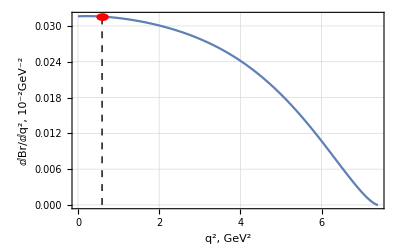

Saving figure to ../TeX/presentation/figs/chi_c2_enu_rho_Ebert.pdf

../TeX/presentation/figs/chi_c2_enu_rho_Ebert.pdf

Saving to file ../TeX/presentation/tables/chi_c2_V_Ebert.tex

% Bc -> chi_c2 + V with [Ebert]
      \begin{tabular}{lcr}
          Paper &:& $\Br  = 0.11\%$ \\
          this      &:& $\Br  = 0.105\%$ \\
		  ratio   &:& $0.955$ \\
      \end{tabular}

```mathematica
out = "chi_c2";
plt = Show[
Plot[100  Ngamma[out, "enu", ffFitRule]/gammaTot,{q2,0,q2Max[out]}],
Graphics[{Dashed, Line[{{($mV)^2,0},{($mV)^2,1}}],
Red, Disk[{($mV)^2,100  Ngamma[out, "enu", ffFitRule]/gammaTot/.{q2->($mV)^2}},Scaled[0.02]]
}]
,Frame->True, FrameLabel->{"q^2, GeV^2","ⅆBr/ⅆq^2, 10^-2GeV^-2"},
GridLines->Automatic
]
SaveFig[out<>"_enu_rho_Ebert", plt]
createCompTable[out, "V", "Ebert"]
```

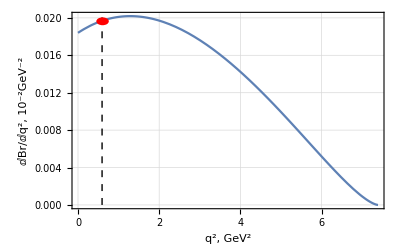

Saving figure to ../TeX/presentation/figs/chi_c2_enu_rho_Wang.pdf

../TeX/presentation/figs/chi_c2_enu_rho_Wang.pdf

Saving to file ../TeX/presentation/tables/chi_c2_V_Wang.tex

% Bc -> chi_c2 + V with [Wang]
      \begin{tabular}{lcr}
          Paper &:& $\Br  = 0.056\pm 0.011\%$ \\
          this      &:& $\Br  = 0.066\%$ \\
		  ratio   &:& $1.171\pm 0.23$ \\
      \end{tabular}

```mathematica
out = "chi_c2";
plt = Show[
Plot[100  Ngamma[out, "enu", ffFitRule$Wang]/gammaTot,{q2,0,q2Max[out]}],
Graphics[{Dashed, Line[{{($mV)^2,0},{($mV)^2,1}}],
Red, Disk[{($mV)^2,100  Ngamma[out, "enu", ffFitRule$Wang]/gammaTot/.{q2->($mV)^2}},Scaled[0.02]]
}]
,Frame->True, FrameLabel->{"q^2, GeV^2","ⅆBr/ⅆq^2, 10^-2GeV^-2"},
GridLines->Automatic
]
SaveFig[out<>"_enu_rho_Wang", plt]
createCompTable[out, "V", "Wang"]
```

### π

```mathematica
out="chi_c0";
Print[createCompTable[out, "P", "Ebert"]];
Print[createCompTable[out, "P", "Wang"]];
```

Saving to file ../TeX/presentation/tables/chi_c0_P_Ebert.tex

% Bc -> chi_c0 + P with [Ebert]
      \begin{tabular}{lcr}
          Paper &:& $\Br  = 0.021\%$ \\
          this      &:& $\Br  = 0.022\%$ \\
		  ratio   &:& $1.034$ \\
      \end{tabular}

Saving to file ../TeX/presentation/tables/chi_c0_P_Wang.tex

% Bc -> chi_c0 + P with [Wang]
      \begin{tabular}{lcr}
          Paper &:& $\Br  = 0.031\pm 0.004\%$ \\
          this      &:& $\Br  = 0.035\%$ \\
		  ratio   &:& $1.127\pm 0.145$ \\
      \end{tabular}

```mathematica
out="chi_c1";
Print[createCompTable[out, "P", "Ebert"]];
Print[createCompTable[out, "P", "Wang"]];
```

Saving to file ../TeX/presentation/tables/chi_c1_P_Ebert.tex

% Bc -> chi_c1 + P with [Ebert]
      \begin{tabular}{lcr}
          Paper &:& $\Br  = 0.02\%$ \\
          this      &:& $\Br  = 0.001\%$ \\
		  ratio   &:& $0.032$ \\
      \end{tabular}

Saving to file ../TeX/presentation/tables/chi_c1_P_Wang.tex

% Bc -> chi_c1 + P with [Wang]
      \begin{tabular}{lcr}
          Paper &:& $\Br  = 0.002\pm 0.\%$ \\
          this      &:& $\Br  = 0.003\%$ \\
		  ratio   &:& $1.339\pm 0.128$ \\
      \end{tabular}

```mathematica
out="chi_c2";
Print[createCompTable[out, "P", "Ebert"]];
Print[createCompTable[out, "P", "Wang"]];
```

Saving to file ../TeX/presentation/tables/chi_c2_P_Ebert.tex

% Bc -> chi_c2 + P with [Ebert]
      \begin{tabular}{lcr}
          Paper &:& $\Br  = 0.038\%$ \\
          this      &:& $\Br  = 0.041\%$ \\
		  ratio   &:& $1.078$ \\
      \end{tabular}

Saving to file ../TeX/presentation/tables/chi_c2_P_Wang.tex

% Bc -> chi_c2 + P with [Wang]
      \begin{tabular}{lcr}
          Paper &:& $\Br  = 0.021\pm 0.005\%$ \\
          this      &:& $\Br  = 0.024\%$ \\
		  ratio   &:& $1.136\pm 0.27$ \\
      \end{tabular}

### nπ

```mathematica
BR["chi_c0", "2pi", "Ebert"]
```

0.0568356

```mathematica
BR["chi_c0", "2pi", "Wang"]
```

0.0935369

```mathematica
Clear[genPlotsNPi];
genPlotsNPi::usage = "genPlotsNPi[nPi]";
Options[genPlotsNPi] = {Position->{1.5, 0.14}, PlotRange->{{0,2},All}};
genPlotsNPi[nPi_, OptionsPattern[]]:=Module[{},
Show[
genNPiPlot["chi_c0", nPi, "Ebert", ShowROOT->False, PlotStyle->Red],
genNPiPlot["chi_c1", nPi, "Ebert", ShowROOT->False, PlotStyle->Blue],
genNPiPlot["chi_c2", nPi, "Ebert", ShowROOT->False, PlotStyle->Black]
,PlotLabel->ToString[nPi]<>"π",
Frame->True, FrameLabel->{"q^2, GeV^2", "ⅆBr/dq^2, 10^-2/GeV^2"}, PlotRange->OptionValue[PlotRange], GridLines->Automatic,
Epilog->Inset[Framed[Column[{
LineLegend[{Red},{"χ_c0"}],
LineLegend[{Blue},{"χ_c1"}],
LineLegend[{Black},{"χ_c2"}]
}]],Offset[{10,20},OptionValue[Position]]]]
]
```

#### 2π

Br[Bc→chi_c0 2pi]:=0.0568356%

Br[Bc→chi_c1 2pi]:=0.0154134%

Br[Bc→chi_c2 2pi]:=0.109309%

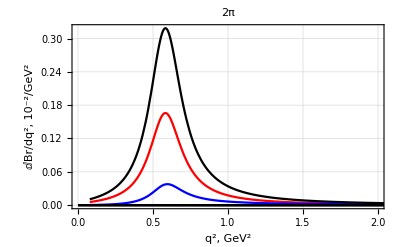

Saving figure to ../TeX/presentation/figs/2pi_q2.pdf

../TeX/presentation/figs/2pi_q2.pdf

```mathematica
nPi = 2;
genPlotsNPi[nPi, Position->{1.7, 0.15}]
SaveFig[ToString[nPi]<>"pi_q2", %]
```

```mathematica
outL = ToString[nPi]<>"pi";
tab = Table[
{BR[out, outL, "Ebert"], BR[out, outL, "Wang"]}
,{out, chiList}];
tab = Prepend[tab,{"[Ebert]", "[Wang]"}];
tab = MapThread[Prepend, {tab, {"","χ_c0","χ_c1","χ_c2"}}];
grid = Grid[tab, Dividers->{2->True,2->True}];
grid = NumberForm[grid, 2];
str = StringReplace[ToString[grid, TeXForm], {"\\chi _"->"\\chi_"}];
str = "$$\n"<>str<>"$$\n";
Print[str];
file = OpenWrite["../TeX/presentation/tables/"<>ToString[nPi]<>"pi.tex"];
WriteString[file, str];
Close[file];
```

$$
\begin{array}{c|cc}
 \text{} & \text{[Ebert]} & \text{[Wang]} \\
\hline
 \chi_{\text{c0}} & 0.057 & 0.094 \\
 \chi_{\text{c1}} & 0.015 & 0.031 \\
 \chi_{\text{c2}} & 0.11 & 0.068 \\
\end{array}$$

#### 3π

Br[Bc→chi_c0 3pi]:=0.0213332%

Br[Bc→chi_c1 3pi]:=0.0156027%

Br[Bc→chi_c2 3pi]:=0.0410091%

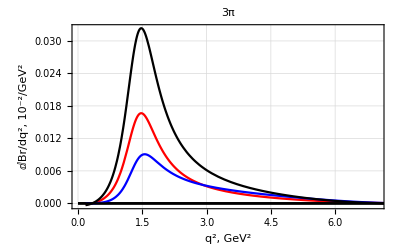

Saving figure to ../TeX/presentation/figs/3pi_q2.pdf

../TeX/presentation/figs/3pi_q2.pdf

```mathematica
nPi = 3;
genPlotsNPi[nPi, Position->{6, 0.015}, PlotRange->{{0, 7}, All}]
SaveFig[ToString[nPi]<>"pi_q2", %]
```

```mathematica
outL = ToString[nPi]<>"pi";
tab = Table[
{BR[out, outL, "Ebert"], BR[out, outL, "Wang"]}
,{out, chiList}];
tab = Prepend[tab,{"[Ebert]", "[Wang]"}];
tab = MapThread[Prepend, {tab, {"","χ_c0","χ_c1","χ_c2"}}];
grid = Grid[tab, Dividers->{2->True,2->True}];
grid = NumberForm[grid, 2];
str = StringReplace[ToString[grid, TeXForm], {"\\chi _"->"\\chi_"}];
str = "$$\n"<>str<>"$$\n";
Print[str];
file = OpenWrite["../TeX/presentation/tables/"<>ToString[nPi]<>"pi.tex"];
WriteString[file, str];
Close[file];
```

$$
\begin{array}{c|cc}
 \text{} & \text{[Ebert]} & \text{[Wang]} \\
\hline
 \chi_{\text{c0}} & 0.021 & 0.034 \\
 \chi_{\text{c1}} & 0.016 & 0.025 \\
 \chi_{\text{c2}} & 0.041 & 0.026 \\
\end{array}$$

#### 5π

Br[Bc→chi_c0 5pi]:=0.0000379145%

Br[Bc→chi_c1 5pi]:=0.0000486109%

Br[Bc→chi_c2 5pi]:=0.0000670549%

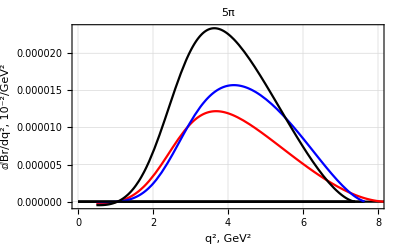

Saving figure to ../TeX/presentation/figs/5pi_q2.pdf

../TeX/presentation/figs/5pi_q2.pdf

```mathematica
nPi =5;
genPlotsNPi[nPi,  Position->{0.5, 1*10^-5}, PlotRange->{{0, 8}, All}]
SaveFig[ToString[nPi]<>"pi_q2", %]
```

```mathematica
outL = ToString[nPi]<>"pi";
tab = Table[
{BR[out, outL, "Ebert"], BR[out, outL, "Wang"]}
,{out, chiList}];
tab = 10^4 tab;
tab = Prepend[tab,{"[Ebert]", "[Wang]"}];
tab = MapThread[Prepend, {tab, {"","χ_c0","χ_c1","χ_c2"}}];
grid = Grid[tab, Dividers->{2->True,2->True}];
grid = NumberForm[grid, 2];
str = StringReplace[ToString[grid, TeXForm], {"\\chi _"->"\\chi_"}];
str = "$$\n"<>str<>"$$\n";
Print[str];
file = OpenWrite["../TeX/presentation/tables/"<>ToString[nPi]<>"pi.tex"];
WriteString[file, str];
Close[file];
```

$$
\begin{array}{c|cc}
 \text{} & \text{[Ebert]} & \text{[Wang]} \\
\hline
 \chi_{\text{c0}} & 0.38 & 0.56 \\
 \chi_{\text{c1}} & 0.49 & 0.63 \\
 \chi_{\text{c2}} & 0.67 & 0.39 \\
\end{array}$$

Br[Bc→chi_c0 5pi]:=0.0000564033%

Br[Bc→chi_c1 5pi]:=0.0000634153%

Br[Bc→chi_c2 5pi]:=0.0000391096%

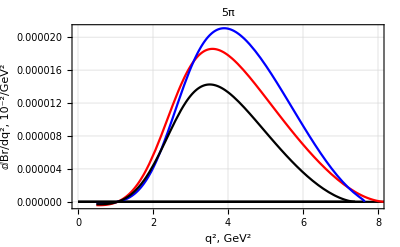

Saving figure to ../TeX/presentation/figs/5pi_q2.pdf

../TeX/presentation/figs/5pi_q2.pdf

```mathematica
genPlotsNPi[5, Position->{0.5, 1*10^-5}, PlotRange->{{0, 8}, All}]
SaveFig["5pi_q2", %]
```

Br[Bc→chi_c0 2pi]:=0.0935369%

Br[Bc→chi_c1 2pi]:=0.0311114%

Br[Bc→chi_c2 2pi]:=0.0683901%

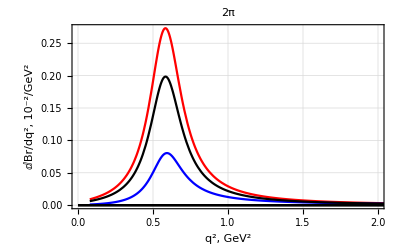

```mathematica
nPi = 2;
Show[
genNPiPlot["chi_c0", nPi, "Ebert", ShowROOT->False, PlotStyle->Red],
genNPiPlot["chi_c1", nPi, "Ebert", ShowROOT->False, PlotStyle->Blue],
genNPiPlot["chi_c2", nPi, "Ebert", ShowROOT->False, PlotStyle->Black]
,PlotLabel->"2π",
Frame->True, FrameLabel->{"q^2, GeV^2", "ⅆBr/dq^2, 10^-2/GeV^2"}, PlotRange->{{0,2},All}, GridLines->Automatic,
Epilog->Inset[Framed[Column[{
LineLegend[{Red},{"χ_c0"}],
LineLegend[{Blue},{"χ_c1"}],
LineLegend[{Black},{"χ_c2"}]
}]],Offset[{10,20},{1.5,0.14}]]]
```

```mathematica
tab=Table[
Flatten[Table[
mode = ToString[nPi]<>"pi";
Table[GetCentralValue[10^3 corrCoeff[out, ffName]*BR[out,mode,ffName]],{out, chiList}]
,{nPi,{2,3,5}}]]
,{ffName,{"Ebert", "Wang"}}];
tab = Round[tab, 0.01];
tab = Prepend[tab, Flatten[Table[{"2π","3π", "5π"}, {chiList//Length}]]];
tab = Prepend[tab,{"χ_c0", SpanFromLeft, SpanFromLeft,"χ_c1", SpanFromLeft, SpanFromLeft,"χ_c2", SpanFromLeft, SpanFromLeft}];
tab = MapThread[Prepend, {tab, {,,"[Ebert]","[Wang]"}}];
grid=Grid[tab, Dividers->{{2->True, 5->True, 8->True}, 3->True}]
fileName="../TeX/presentation/tables/tabNPI.tex";
Print["Saving table to ", fileName];
file = OpenWrite[fileName];
WriteString[file, "$$\n"<>ToString[grid, TeXForm]<>"$$\n"];
Close[file];
```

| χ_c0 |  |  | χ_c1 |  |  | χ_c2 |  | 
 | 2π | 3π | 5π | 2π | 3π | 5π | 2π | 3π | 5π
[Ebert] | 56.24 | 15.4 | 109.16 | 21.11 | 15.59 | 40.95 | 0.04 | 0.05 | 0.07
[Wang] | 90.95 | 30.47 | 69.4 | 33.5 | 24.43 | 26.63 | 0.05 | 0.06 | 0.04

Saving table to ../TeX/presentation/tables/tabNPI.tex

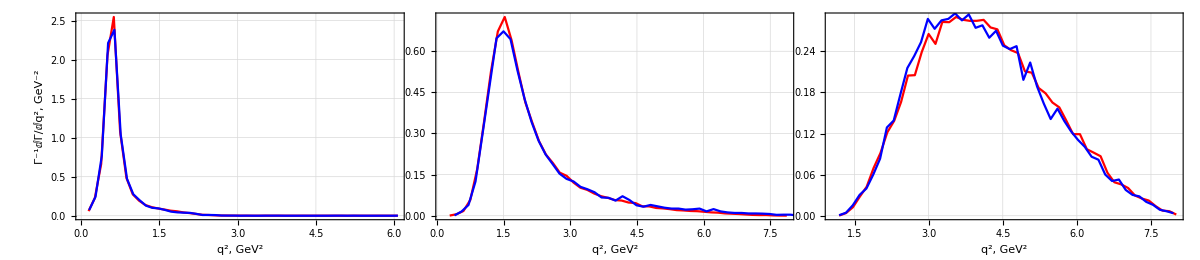

Saving figure to ../TeX/presentation/figs/chi_c0_nPi_q2.pdf

```mathematica
out="chi_c0";
(*nPi=5;*)
plot = genPlotsNPi[out]
SaveFig[out<>"_nPi_q2", plot];
```

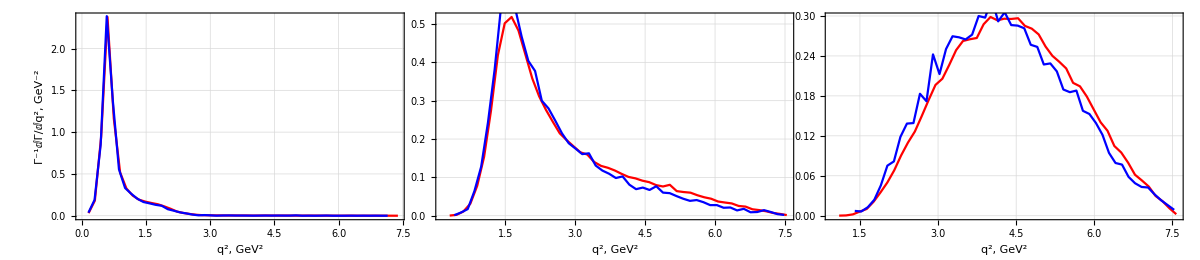

Saving figure to ../TeX/presentation/figs/chi_c1_nPi_q2.pdf

```mathematica
out="chi_c1";
(*nPi=5;*)
plot = genPlotsNPi[out]
SaveFig[out<>"_nPi_q2", plot];
```

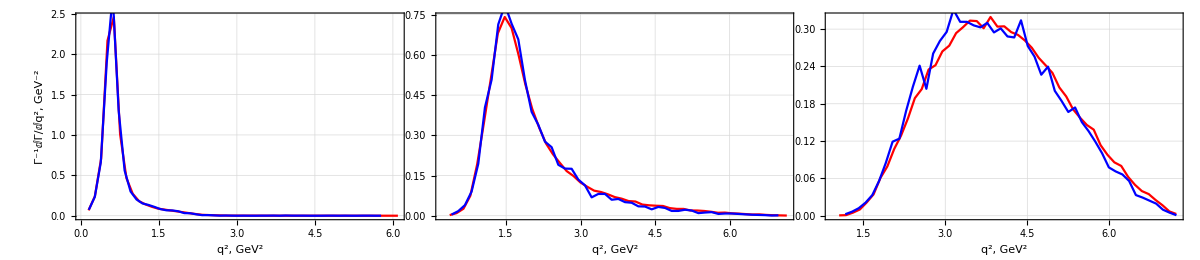

Saving figure to ../TeX/presentation/figs/chi_c2_nPi_q2.pdf

```mathematica
out="chi_c2";
(*nPi=5;*)
plot = genPlotsNPi[out]
SaveFig[out<>"_nPi_q2", plot];
```

### final tables

#### Predictions

```mathematica
tab = Table[
Flatten[Table[BR[out,outL, ffName],{out, chiList},{ffName,{"Ebert","Wang"}}]]
,{outL,{"enu","P","V","2pi", "3pi", "5pi"}}];
tab = MapThread[Prepend, {tab,{"enu","P","V","2pi", "3pi", "5pi"}}];
(**)
str = ToString[NumberForm[tab,3, ScientificNotationThreshold->{-7,3}], TeXForm];
str = StringReplace[str, {"\\text{"->"", "enu}"->"e\\nu", "P}"->"\\pi", "V}"->"\\rho", "pi}"->"\\pi",
"\\left("->"", "\\right)"->"", 
"\\begin{array}{ccccccc}" -> "\\begin{array}{r|rr|rr|rr}
  &\\multicolumn{2}{c}{\\chi_{c0}} & \\multicolumn{2}{c}{\\chi_{c1}} & \\multicolumn{2}{c}{\\chi_{c2}} \\\\
   & \\text{[Ebert]} & \\text{[Wang]} & \\text{[Ebert]} & \\text{[Wang]} & \\text{[Ebert]} & \\text{[Wang]} \\\\
\\hline"}
];
str = "$$"<>str<>"$$"
(**)
file = OpenWrite["../TeX/presentation/tables/sum_table.tex"];
WriteString[file, str];
Close[file];
```

$$
\begin{array}{r|rr|rr|rr}
  &\multicolumn{2}{c}{\chi_{c0}} & \multicolumn{2}{c}{\chi_{c1}} & \multicolumn{2}{c}{\chi_{c2}} \\
   & \text{[Ebert]} & \text{[Wang]} & \text{[Ebert]} & \text{[Wang]} & \text{[Ebert]} & \text{[Wang]} \\
\hline
 e\nu & 0.0889 & 0.138 & 0.0822 & 0.115 & 0.16 & 0.0971 \\
 \pi & 0.0217 & 0.0349 & 0.000644 & 0.00281 & 0.041 & 0.0238 \\
 \rho & 0.0547 & 0.0901 & 0.0127 & 0.0269 & 0.105 & 0.0656 \\
 2\pi & 0.0568 & 0.0935 & 0.0154 & 0.0311 & 0.109 & 0.0684 \\
 3\pi & 0.0213 & 0.0345 & 0.0156 & 0.0249 & 0.041 & 0.0262 \\
 5\pi & 0.0000379 & 0.0000564 & 0.0000486 & 0.0000634 & 0.0000671 & 0.0000391 \\
\end{array}
$$

### Original BRs

```mathematica
tab = Table[
Flatten[Table[$BR[out,outL, ffName],{out, chiList},{ffName,{"Ebert","Wang"}}]]
,{outL,{"enu","P","V"}}];
tab = MapThread[Prepend, {tab,{"enu","P","V"}}];
str = ToString[NumberForm[tab,3, ScientificNotationThreshold->{-7,3}], TeXForm];
str = StringReplace[str, {"\\text{"->"", "enu}"->"e\\nu", "P}"->"\\pi", "V}"->"\\rho", "pi}"->"\\pi",
"\\left("->"", "\\right)"->"", 
"\\begin{array}{ccccccc}" -> "\\begin{array}{r|rr|rr|rr}
  &\\multicolumn{2}{c}{\\chi_{c0}} & \\multicolumn{2}{c}{\\chi_{c1}} & \\multicolumn{2}{c}{\\chi_{c2}} \\\\
   & \\text{[Ebert]} & \\text{[Wang]} & \\text{[Ebert]} & \\text{[Wang]} & \\text{[Ebert]} & \\text{[Wang]} \\\\
\\hline"}
];
str = "$$"<>str<>"$$"
(**)
file = OpenWrite["../TeX/presentation/tables/papers_table.tex"];
WriteString[file, str];
Close[file];
```

$$
\begin{array}{r|rr|rr|rr}
  &\multicolumn{2}{c}{\chi_{c0}} & \multicolumn{2}{c}{\chi_{c1}} & \multicolumn{2}{c}{\chi_{c2}} \\
   & \text{[Ebert]} & \text{[Wang]} & \text{[Ebert]} & \text{[Wang]} & \text{[Ebert]} & \text{[Wang]} \\
\hline
 e\nu & 0.087 & 0.13\pm 0.03 & 0.082 & 0.11\pm 0.03 & 0.16 & 0.1\pm 0.03 \\
 \pi & 0.021 & 0.031\pm 0.004 & 0.02 & 0.0021\pm 0.0002 & 0.038 & 0.021\pm 0.005 \\
 \rho & 0.058 & 0.076\pm 0.009 & 0.015 & 0.023\pm 0.002 & 0.11 & 0.056\pm 0.011 \\
\end{array}
$$

#### Fractions

```mathematica
tab = Table[
Flatten[Table[BR[out,outL, ffName]/$BR[out,outL, ffName],{out, chiList},{ffName,{"Ebert","Wang"}}]]
,{outL,{"enu","P","V"}}];
tab = MapThread[Prepend, {tab,{"enu","P","V"}}];
str = ToString[NumberForm[tab,3, ScientificNotationThreshold->{-7,3}], TeXForm];
str = StringReplace[str, {"\\text{"->"", "enu}"->"e\\nu", "P}"->"\\pi", "V}"->"\\rho", "pi}"->"\\pi",
"\\left("->"", "\\right)"->"", 
"\\begin{array}{ccccccc}" -> "\\begin{array}{r|rr|rr|rr}
  &\\multicolumn{2}{c}{\\chi_{c0}} & \\multicolumn{2}{c}{\\chi_{c1}} & \\multicolumn{2}{c}{\\chi_{c2}} \\\\
   & \\text{[Ebert]} & \\text{[Wang]} & \\text{[Ebert]} & \\text{[Wang]} & \\text{[Ebert]} & \\text{[Wang]} \\\\
\\hline"}
];
str = "$$"<>str<>"$$"
(**)
file = OpenWrite["../TeX/presentation/tables/ratios_table.tex"];
WriteString[file, str];
Close[file];
```

$$
\begin{array}{r|rr|rr|rr}
  &\multicolumn{2}{c}{\chi_{c0}} & \multicolumn{2}{c}{\chi_{c1}} & \multicolumn{2}{c}{\chi_{c2}} \\
   & \text{[Ebert]} & \text{[Wang]} & \text{[Ebert]} & \text{[Wang]} & \text{[Ebert]} & \text{[Wang]} \\
\hline
 e\nu & 1.02 & 1.06\pm 0.244 & 1. & 1.04\pm 0.284 & 1. & 0.971\pm 0.291 \\
 \pi & 1.03 & 1.13\pm 0.145 & 0.0322 & 1.34\pm 0.128 & 1.08 & 1.14\pm 0.27 \\
 \rho & 0.943 & 1.19\pm 0.14 & 0.845 & 1.17\pm 0.102 & 0.955 & 1.17\pm 0.23 \\
\end{array}
$$

## Combined Tables

```mathematica
tab = Table[
Flatten[Table[corrBR[out,outL, ffName],{out, chiList},{ffName,{"Ebert","Wang"}}]]
,{outL,{"enu","P","V","2pi", "3pi", "5pi"}}];
tab = Round[tab,0.0001];
colNames = Flatten[Table[out<>" ["<>ffName<>"]",{out, chiList},{ffName,{"Ebert","Wang"}}]];
Print["Predictions Table\n",
Grid[
MapThread[Prepend, {Prepend[tab, colNames],{" ","enu","P","V","2pi", "3pi", "5pi"}}]
,Dividers->{{2->True, 4->True, 6->True}, {2->True}}, Alignment->Right]
]
```

Predictions Table
  | chi_c0 [Ebert] | chi_c0 [Wang] | chi_c1 [Ebert] | chi_c1 [Wang] | chi_c2 [Ebert] | chi_c2 [Wang]
enu | 0.087 | 0.13±0.03 | 0.082 | 0.11±0.03 | 0.16 | 0.1±0.03
P | 0.0213 | 0.033±0.0076 | 0.0006 | 0.0027±0.0007 | 0.0408 | 0.0246±0.0074
V | 0.0535 | 0.0852±0.0197 | 0.0127 | 0.0258±0.007 | 0.1048 | 0.0675±0.0203
2pi | 0.0556 | 0.0884±0.0204 | 0.0154 | 0.0298±0.0081 | 0.109 | 0.0704±0.0211
3pi | 0.0209 | 0.0326±0.0075 | 0.0156 | 0.0239±0.0065 | 0.0409 | 0.027±0.0081
5pi | 0. | 0.0001±0. | 0. | 0.0001±0. | 0.0001 | 0.±0.

```mathematica
tab = Table[
Flatten[Table[$BR[out,outL, ffName],{out, chiList},{ffName,{"Ebert","Wang"}}]]
,{outL,{"enu","P","V"}}];
colNames = Flatten[Table[out<>" ["<>ffName<>"]",{out, chiList},{ffName,{"Ebert","Wang"}}]];
Print["Papers' table\n",
Grid[
MapThread[Prepend, {Prepend[tab, colNames],{" ","enu","P","V"}}]
,Dividers->{None, {2->True}}, Alignment->Right]
]
```

Papers' table
  | chi_c0 [Ebert] | chi_c0 [Wang] | chi_c1 [Ebert] | chi_c1 [Wang] | chi_c2 [Ebert] | chi_c2 [Wang]
enu | 0.087 | 0.13±0.03 | 0.082 | 0.11±0.03 | 0.16 | 0.1±0.03
P | 0.021 | 0.031±0.004 | 0.02 | 0.0021±0.0002 | 0.038 | 0.021±0.005
V | 0.058 | 0.076±0.009 | 0.015 | 0.023±0.002 | 0.11 | 0.056±0.011

```mathematica
ffName="Ebert";
tab = Table[
Flatten[Table[{
corrBR[out,outL, ffName], $BR[out, outL, ffName],corrBR[out,outL, ffName]/$BR[out, outL, ffName]},{out, chiList}]]
,{outL,{"enu","P","V"}}];
tab = Round[tab,0.0001];
colNames = Flatten[Table[{"this","work","this/work"},{out, chiList}]];
Print["Comparison:",ffName,"\n",
Grid[
MapThread[Prepend, {Prepend[tab, colNames],{" ","enu","P","V"}}]
,Dividers->{{5->True,8->True}, {2->True}}, Alignment->Right]
]
```

Comparison:Ebert
  | this | work | this/work | this | work | this/work | this | work | this/work
enu | 0.087 | 0.087 | 1. | 0.082 | 0.082 | 1. | 0.16 | 0.16 | 1.
P | 0.0213 | 0.021 | 1.012 | 0.0006 | 0.02 | 0.0321 | 0.0408 | 0.038 | 1.0747
V | 0.0535 | 0.058 | 0.9232 | 0.0127 | 0.015 | 0.8435 | 0.1048 | 0.11 | 0.9528

```mathematica
ffName="Wang";
tab = Table[
Flatten[Table[{
corrBR[out,outL, ffName], $BR[out, outL, ffName],corrBR[out,outL, ffName]/$BR[out, outL, ffName]},{out, chiList}]]
,{outL,{"enu","P","V"}}];
tab = Round[tab,0.0001];
colNames = Flatten[Table[{"this","work","this/work"},{out, chiList}]];
Print["Comparison:",ffName,"\n",
Grid[
MapThread[Prepend, {Prepend[tab, colNames],{" ","enu","P","V"}}]
,Dividers->{{5->True,8->True}, {2->True}}, Alignment->Right]
]
```

Comparison:Wang
  | this | work | this/work | this | work | this/work | this | work | this/work
enu | 0.13±0.03 | 0.13±0.03 | 1.±0.3264 | 0.11±0.03 | 0.11±0.03 | 1.±0.3857 | 0.1±0.03 | 0.1±0.03 | 1.±0.4243
P | 0.033±0.0076 | 0.031±0.004 | 1.0652±0.2816 | 0.0027±0.0007 | 0.0021±0.0002 | 1.2845±0.3711 | 0.0246±0.0074 | 0.021±0.005 | 1.1694±0.4479
V | 0.0852±0.0197 | 0.076±0.009 | 1.1213±0.2908 | 0.0258±0.007 | 0.023±0.002 | 1.123±0.3215 | 0.0675±0.0203 | 0.056±0.011 | 1.2061±0.4325